```mathematica
(* 绘图函数 *)
PlotG[number_]:={ParametricPlot[{Re[number],Im[number]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All,ImageSize->Medium]
Plot[{Re[number],Im[number]},{ξ,0,2π},PlotRange->All,ImageSize->Medium]
,Print["Stability interval length"->Re[number]/.ξ->π]};
termstop[k_]:=ⅇ^((k+1 )*ⅈ ξ)-ⅇ^(k*ⅈ ξ);
```

```mathematica
part={(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,2,2}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,3,3}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,4,4}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,5,5}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,6,6}])^2};
```

```mathematica
(* α优化之后 *)
Remove[α,OptimCod,k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
o=4;k=1;t=0;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
p=(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,o+1,o+1}])^2;
OptimCod=t*bs+(1-t)*p;
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{OptimCod[[1]],cons},R,Method->Automatic];(*,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25*)
sol[[2]];
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b];
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)((k+1)^(o+1)-k^(o+1)-(o+1)*∑_(i=0)^k result[[1,k-i+1,2]]*i^o);
Constanterror=Subscript[C, o+1]/σ[1];
{t,-Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π,Subscript[C, o+1]/σ[1]}
(*Print["C"->Constanterror];*)
(*PlotG[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]];*)
```

{{{0.,0.163339,-1.06365×10^-10},{0.05,0.163496,0.000730994},{0.1,0.163669,0.00154321},{0.15,0.25181,0.268885},{0.2,0.25181,0.268885},{0.25,0.164334,0.00462963},{0.3,0.16462,0.00595238},{0.35,0.251809,0.26887},{0.4,0.16534,0.00925926},{0.45,0.165801,0.0113636},{0.5,0.251809,0.26887},{0.55,0.167045,0.0169753},{0.6,0.168112,0.0217296},{0.65,0.169037,0.0257937},{0.7,0.170562,0.0324074},{0.75,0.172745,0.0416667},{0.8,0.176125,0.0555556},{0.85,0.182063,0.0787037},{0.9,0.195228,0.125},{0.95,0.249307,0.263889},{1.,0.75,0.598611}},{{0.,0.136346,-3.38438×10^-9},{0.05,0.469193,0.000121831},{0.1,0.469233,0.000257202},{0.15,0.469277,0.000408491},{0.2,0.469327,0.000578703},{0.25,0.469384,0.000771605},{0.3,0.469449,0.00099133},{0.35,0.469523,0.00124644},{0.4,0.469611,0.00154321},{0.45,0.469714,0.00189394},{0.5,0.469838,0.00231481},{0.55,0.469989,0.00282922},{0.6,0.470178,0.00347222},{0.65,0.470422,0.00429891},{0.7,0.470748,0.00540118},{0.75,0.471204,0.00694442},{0.8,0.47189,0.00925925},{0.85,0.473039,0.0131173},{0.9,0.475352,0.0208333},{0.95,0.48243,0.0439815},{1.,1.1819,1.01208}},{{0.,0.151635,1.06108×10^-13},{0.05,0.792372,0.0000380812},{0.1,0.739646,0.00253463},{0.15,0.792395,0.000127683},{0.2,0.792409,0.000180886},{0.25,0.792425,0.000241181},{0.3,0.792443,0.00031009},{0.35,0.781329,0.000866815},{0.4,0.792488,0.000482362},{0.45,0.792517,0.000591989},{0.5,0.792551,0.000723456},{0.55,0.792593,0.00088433},{0.6,0.792646,0.00108531},{0.65,0.793062,0.00304915},{0.7,0.793175,0.00343007},{0.75,0.79293,0.00217063},{0.8,0.793323,0.00510114},{0.85,0.793436,0.00410008},{0.9,0.79407,0.00651189},{0.95,0.796794,0.017223},{1.,1.5868,1.64707}},{{0.,0.16708,-7.12438×10^-13},{0.05,1.1055,0.0000156738},{0.1,1.10551,0.0000330966},{0.15,1.10551,0.0000525652},{0.2,1.10551,0.0000744674},{0.25,1.10552,0.0000992899},{0.3,1.10553,0.000127658},{0.35,1.10553,0.000160293},{0.4,0.799032,0.00254467},{0.45,1.10555,0.000243711},{0.5,0.749415,0.00388406},{0.55,1.10557,0.000364063},{0.6,1.10559,0.000446804},{0.65,1.10561,0.000553175},{0.7,1.10564,0.000695028},{0.75,1.10569,0.000893606},{0.8,1.10575,0.00119147},{0.85,1.10585,0.00168793},{0.9,1.10606,0.00268082},{0.95,1.10505,0.0114329},{1.,1.97092,2.57716}},{{0.,0.785764,0.00903895},{0.05,0.786952,0.0110318},{0.1,0.788253,0.0210965},{0.15,1.05871,0.00896034},{0.2,1.40516,0.0000359852},{0.25,1.06954,0.00298735},{0.3,1.40516,0.0000616889},{0.35,1.40516,0.0000775065},{0.4,1.40517,0.0000959566},{0.45,1.40517,0.00011777},{0.5,1.40517,0.000143941},{0.55,1.40518,0.000175885},{0.6,1.40519,0.000215911},{0.65,1.40519,0.000267319},{0.7,1.40521,0.000335854},{0.75,1.40522,0.000431818},{0.8,1.40525,0.000575763},{0.85,1.40528,0.000815639},{0.9,1.40536,0.00129547},{0.95,1.4056,0.00273487},{1.,2.33998,3.87883}},{{0.,0.116335,-3.63798×10^-13},{0.05,1.69289,4.07369×10^-6},{0.1,1.69289,8.6×10^-6},{0.15,1.69289,0.0000136581},{0.2,1.69289,0.0000193446},{0.25,1.69289,0.0000257981},{0.3,1.30816,0.0343257},{0.35,1.69289,0.0000416724},{0.4,1.31695,0.0765858},{0.45,1.56641,0.0342884},{0.5,1.32336,0.0872076},{0.55,1.3243,0.0964598},{0.6,1.6929,0.0001161},{0.65,1.6929,0.000143743},{0.7,1.69291,0.0001806},{0.75,1.69291,0.0002322},{0.8,1.69292,0.0003096},{0.85,1.69294,0.000438601},{0.9,1.6738,0.0124807},{0.95,1.69307,0.0014706},{1.,1.56949,1.55897}},{{0.,0.266296,2.18279×10^-12},{0.05,0.732595,-0.00562909},{0.1,0.753814,0.00200536},{0.15,0.640008,0.00426549},{0.2,0.959699,0.0000109393},{0.25,0.821796,0.0213068},{0.3,0.807438,0.0122909},{0.35,0.803007,-0.000913869},{0.4,0.839738,0.0197242},{0.45,0.806943,-0.00803889},{0.5,1.97093,0.0000449603},{0.55,0.892156,0.0368362},{0.6,0.862613,0.0179157},{0.65,0.924384,0.0183789},{0.7,0.904276,0.0399747},{0.75,1.97094,0.000134881},{0.8,0.859538,0.0734789},{0.85,1.97095,0.000254775},{0.9,1.97097,0.000404643},{0.95,1.97101,0.000854245},{1.,3.04804,8.00092}}}

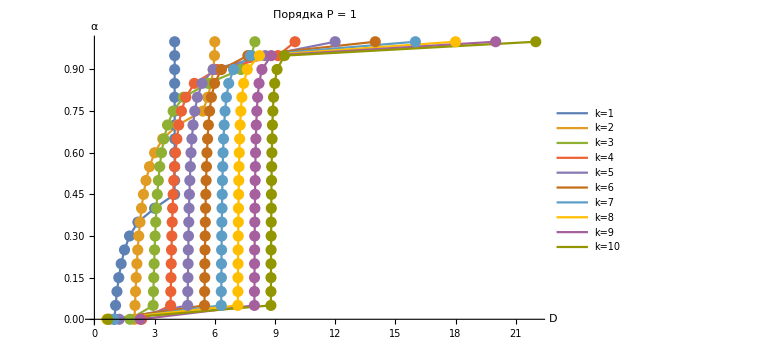

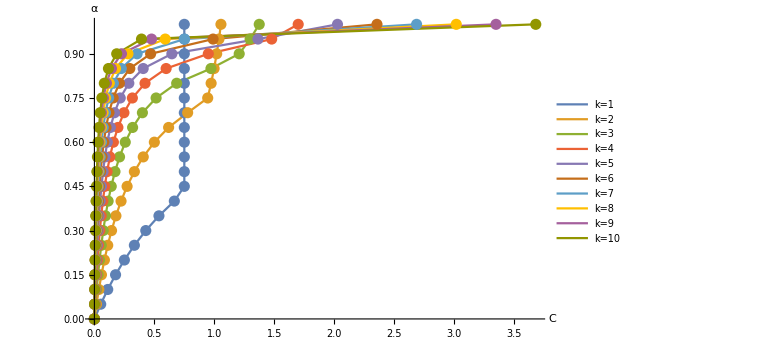

```mathematica
datak1to10o1={{{0.,1.,0.},{0.05,1.0555555555555558,0.0526315789473686},{0.1,1.125,0.11111111111111116},{0.15000000000000002,1.21428571099818,0.17647058600568613},{0.2,1.3333333235429277,0.24999999449289712},{0.25,1.499999999999999,0.3333333333333324},{0.30000000000000004,1.7499999785186586,0.42857142155711314},{0.35000000000000003,2.166666666666653,0.5384615384615355},{0.4,2.9999999999999996,0.6666666666666664},{0.45,3.9999999999999893,0.7499999999999993},{0.5,4.,0.75},{0.55,4.,0.75},{0.6000000000000001,4.,0.75},{0.65,4.,0.75},{0.7000000000000001,4.,0.75},{0.75,4.,0.75},{0.8,4.,0.75},{0.8500000000000001,4.,0.75},{0.9,4.,0.75},{0.9500000000000001,4.,0.75},{1.,4.,0.75}},{{0.,1.9994183948126807,0.},{0.05,2.0236686390532546,0.017543859649122865},{0.1,2.0506329113924053,0.0370370370370372},{0.15000000000000002,2.0816326530612237,0.05882352941176404},{0.2,2.11764705882353,0.08333333333333397},{0.25,2.16,0.11111111111111163},{0.30000000000000004,2.2105263157894735,0.14285714285714282},{0.35000000000000003,2.271844660194174,0.17948717948717927},{0.4,2.3478260869565206,0.22222222222222193},{0.45,2.4444444444444446,0.272727272727273},{0.5,2.571428571428571,0.3333333333333331},{0.55,2.745762711864407,0.40740740740740755},{0.6000000000000001,3.0000000082925573,0.500000002764186},{0.65,3.4054054054053995,0.6190476190476175},{0.7000000000000001,4.153846153846155,0.7777777777777781},{0.75,5.404701989372699,0.9451365350535652},{0.8,5.647741037960197,0.9736037540334934},{0.8500000000000001,5.8187933518214985,0.9983663319787857},{0.9,5.926916919792357,1.0199728418760363},{0.9500000000000001,5.983502397621351,1.038900432658531},{1.,5.999999999999999,1.0555555555555556}},{{0.,1.7743445627212378,-4.440892098500625*^-16},{0.05,2.9274311354524927,0.009030151329147081},{0.1,2.9422586611640025,0.019063652805979554},{0.15000000000000002,2.9590093633471333,0.03027756622126087},{0.2,2.978083352821737,0.04289321881345299},{0.25,2.9999999999999987,0.05719095841793552},{0.30000000000000004,3.0254459466573045,0.07353123225163352},{0.35000000000000003,3.0553483431804023,0.0923853943674362},{0.4,3.0909902576697315,0.11438191683587282},{0.45,3.1341995953622135,0.14037780702584482},{0.5,3.187672642712108,0.17157287525380924},{0.55,3.2555592434594276,0.20970018086576742},{0.6000000000000001,3.344594882827518,0.2573593128807153},{0.65,3.4664860411090688,0.31863533975707586},{0.7000000000000001,3.6435337094166966,0.4003367089255564},{0.75,3.924123217214741,0.5147186257614296},{0.8,4.436621312300577,0.6862915010152397},{0.8500000000000001,5.671034884762731,0.9722462931049232},{0.9,7.2984000544558745,1.2079589524236185},{0.9500000000000001,7.831319534112508,1.2989263782412848},{1.,8.,1.375}},{{0.,2.357666519677977,0.},{0.05,3.7972940261834816,0.005556354160010991},{0.1,3.806715968571725,0.011730312111120966},{0.15000000000000002,3.8173016709553704,0.018630495705896696},{0.2,3.8292811790522014,0.02639320225002085},{0.25,3.84294917388403,0.035190936333361136},{0.30000000000000004,3.8586897039028125,0.04524548957146469},{0.35000000000000003,3.8770128421199557,0.05684689715389182},{0.4,3.898610999168043,0.07038187266672223},{0.45,3.9244483953773868,0.086377752818251},{0.5,3.9559089499998557,0.1055728090000843},{0.55,3.9950525189703248,0.12903343322232352},{0.6000000000000001,4.045084971874737,0.1583592135001259},{0.65,4.111283943649195,0.19606378814301362},{0.7000000000000001,4.202994894030598,0.24633655433352958},{0.75,4.338485732733601,0.3167184270002518},{0.8,4.558933436255707,0.4222912360003379},{0.8500000000000001,4.980736491113634,0.5982459176671436},{0.9,6.111667729600601,0.9501552810007574},{0.9500000000000001,9.150530675671996,1.478777867229879},{1.,10.,1.6999999999999997}},{{0.,1.2389330291701681,0.},{0.05,4.6485897386358435,0.003778777353920404},{0.1,4.655113005517712,0.007977418858275518},{0.15000000000000002,4.662425415025968,0.012670018186674348},{0.2,4.670679384443654,0.017949192431121475},{0.25,4.680069283048468,0.023932256574828326},{0.30000000000000004,4.690846932524303,0.030770044167637053},{0.35000000000000003,4.703344528251027,0.03865979908241801},{0.4,4.718009485782657,0.047864513149658436},{0.45,4.735459138076254,0.058742811592765065},{0.5,4.756569860407206,0.07179676972448945},{0.55,4.782628867051062,0.08775160744104493},{0.6000000000000001,4.815606920675542,0.10769515458673773},{0.65,4.858681519464664,0.1333368580597689},{0.7000000000000001,4.917327476706862,0.1675257960238116},{0.75,5.001851166488378,0.21539030917347185},{0.8,5.134229169262949,0.28718707889796224},{0.8500000000000001,5.3711487692998165,0.4068483617721146},{0.9,5.917253462930164,0.6461709275204176},{0.9500000000000001,8.514293106454353,1.364138624765327},{1.,12.,2.0277777777777777}},{{0.,0.7392070251392827,0.},{0.05,5.488776783294617,0.002741846505351474},{0.1,5.493562279651822,0.005788342622407684},{0.15000000000000002,5.498920660202582,0.009193250047356827},{0.2,5.504961346709843,0.013023770900423063},{0.25,5.511823522042495,0.017365027867227486},{0.30000000000000004,5.51968698659962,0.022326464400721942},{0.35000000000000003,5.528788141057822,0.028051198862449674},{0.4,5.539444160722576,0.034730055734454084},{0.45,5.552090717133518,0.04262325021956226},{0.5,5.567343016564693,0.052095083601686895},{0.55,5.586098901747138,0.06367176884650583},{0.6000000000000001,5.609722222962992,0.07814262540252766},{0.65,5.640390258507959,0.09674801240313351},{0.7000000000000001,5.681806412844554,0.12155519507060214},{0.75,5.740821450965856,0.15628525080506073},{0.8,5.8316790237761476,0.2083803344067494},{0.8500000000000001,5.989672411387923,0.295205473742893},{0.9,6.332812888526874,0.46885575241518196},{0.9500000000000001,7.64708777802863,0.9898065884320546},{1.,14.,2.357142857142858}},{{0.,0.9638513801422565,0.},{0.05,6.321826779371206,0.0020824278892934696},{0.1,6.325487677469433,0.004396236655177079},{0.15000000000000002,6.329584290252316,0.006982258217044011},{0.2,6.334199326856875,0.009891532474146201},{0.25,6.339437844039425,0.013188709965527678},{0.30000000000000004,6.345435340730082,0.016956912812819525},{0.35000000000000003,6.352369645692584,0.021304839175083867},{0.4,6.360478847653835,0.02637741993105448},{0.45,6.370089182829907,0.0323722880972035},{0.5,6.381659989295109,0.039566129896579455},{0.55,6.39585929775897,0.04835860320693366},{0.6000000000000001,6.413697538494086,0.0593491948448719},{0.65,6.436779153753077,0.0734799555222203},{0.7000000000000001,6.467814314710338,0.09232096975868666},{0.75,6.511769737747293,0.11869838968974025},{0.8,6.578834617308594,0.15826451958631968},{0.8500000000000001,6.693732820485511,0.22420806941395277},{0.9,6.936005066474883,0.3560951690692206},{0.9500000000000001,7.780864371889921,0.751756468035021},{1.,16.,2.6875}},{{0.,0.618128072345918,-1.7763568394002473*^-14},{0.05,7.150030586356336,0.0016363791645126469},{0.1,7.152921734505685,0.003454578236194549},{0.15000000000000002,7.156155785867064,0.005486683081016963},{0.2,7.159797591028177,0.007772801031439515},{0.25,7.163929453745783,0.010363734708590757},{0.30000000000000004,7.168657425926857,0.013324801768185068},{0.35000000000000003,7.174120538983682,0.01674141760618398},{0.4,7.18050470426308,0.0207274694171744},{0.45,7.188064291316033,0.025438257921079448},{0.5,7.197156833278872,0.03109120412575806},{0.55,7.208301227437573,0.03800036059815071},{0.6000000000000001,7.222280348079959,0.04663680618864419},{0.65,7.240333372037983,0.05774080766213176},{0.7000000000000001,7.264544931707144,0.07254614296011395},{0.75,7.298714430708622,0.09327361237728837},{0.8,7.3505756601540515,0.12436481650305353},{0.8500000000000001,7.438668454936002,0.1761834900459913},{0.9,7.6213440795407745,0.2798208371318723},{0.9500000000000001,8.227485223439025,0.5907328783895044},{1.,17.999999999999986,3.0185185185185133}},{{0.,2.2839264089476123,0.},{0.05,7.974797457031269,0.0013202963651011148},{0.1,7.977138561231829,0.0027872923263227993},{0.15000000000000002,7.979756716587293,0.004426876047688209},{0.2,7.982704196379727,0.00627140773422852},{0.25,7.986047306837886,0.008361876978970171},{0.30000000000000004,7.989871434902227,0.010750984687250666},{0.35000000000000003,7.994288443758803,0.013507647427571715},{0.4,7.9994477971641205,0.0167237539579439},{0.45,8.005553807162626,0.020524607130205656},{0.5,8.01289333479901,0.025085630936915848},{0.55,8.021882165135708,0.030660215589563215},{0.6000000000000001,8.033146603096505,0.03762844640537111},{0.65,8.047676020588872,0.046587600311417184},{0.7000000000000001,8.06713053212843,0.05853313885280184},{0.75,8.094525403948042,0.0752568928107493},{0.8,8.135968357435527,0.1003425237476669},{0.8500000000000001,8.20599109716541,0.1421519086425285},{0.9,8.349715839785233,0.22577067843224435},{0.9500000000000001,8.8127726989479,0.4766269878014171},{1.,19.999999999999993,3.349999999999997}},{{0.,0.664224908925395,-1.7763568394002486*^-14},{0.05,8.79704012508057,0.0010879379826604918},{0.1,8.798974643491993,0.0022969108693473577},{0.15000000000000002,8.801137624729481,0.003648034910138877},{0.2,8.803572461491122,0.005168181507940518},{0.25,8.80633327298762,0.006890827478720498},{0.30000000000000004,8.809490523206055,0.00885951335318325},{0.35000000000000003,8.813136494134405,0.011131183443747977},{0.4,8.817393943023712,0.013781465216069932},{0.45,8.822430779753843,0.016913616401541983},{0.5,8.828482584943789,0.020672197824104902},{0.55,8.835890732735326,0.02526615121548125},{0.6000000000000001,8.845168124446241,0.031008410683810446},{0.65,8.857124920119627,0.03839134990578863},{0.7000000000000001,8.873117461361769,0.048235128256244764},{0.75,8.895604576623109,0.06201659347231113},{0.8,8.929549773878442,0.0826887912964178},{0.8500000000000001,8.986704490755088,0.117142454336598},{0.9,9.103237343144748,0.18604978039634548},{0.9500000000000001,9.471703200403113,0.39277175865799663},{1.,22.,3.6818181818181834}}};
k1to10Do1=ListLinePlot[Table[datak1to10o1[[x,All,{2,1}]],{x,1,10}],Joined->True,PlotLegends->{"k=1","k=2","k=3","k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[D],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 1",18]]
k1to10Co1=ListLinePlot[Table[datak1to10o1[[x,All,{3,1}]],{x,1,10}],Joined->True,PlotLegends->{"k=1","k=2","k=3","k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[C],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All]
```

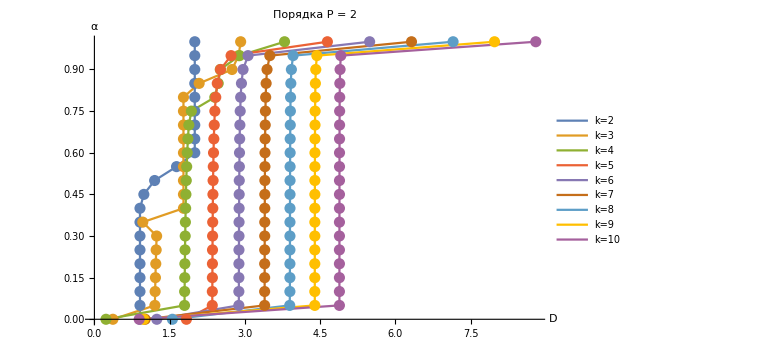

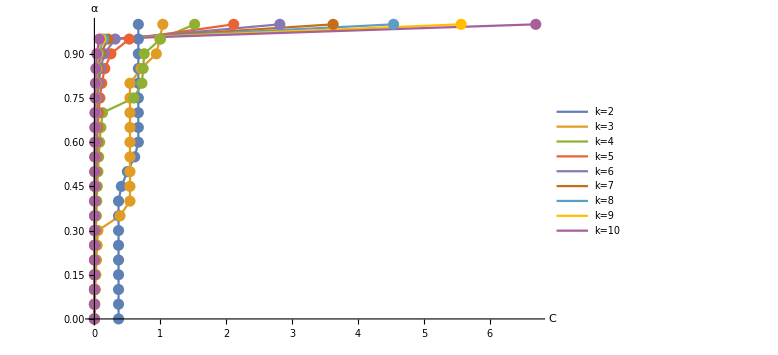

```mathematica
datak2to10o2={{{0.,0.908248290463863,0.3661564094498442},{0.05,0.9082483053182182,0.36615643150758415},{0.1,0.9082483054158302,0.3661564273689421},{0.15000000000000002,0.9082482904638627,0.3661564094498443},{0.2,0.9082482996881794,0.36615642171639345},{0.25,0.9082482993300184,0.36615642138564886},{0.30000000000000004,0.9082483095109729,0.3661564338003639},{0.35000000000000003,0.9082483246297417,0.3661564367755806},{0.4,0.9082483984258528,0.3661564840427621},{0.45,0.9852843830167368,0.40919898545516137},{0.5,1.2000000000000004,0.4999999999999988},{0.55,1.6363636363636342,0.6111111111111105},{0.6000000000000001,2.,0.6666666666666666},{0.65,1.9999999189221296,0.6666666846790057},{0.7000000000000001,1.999999972652152,0.6666666875574739},{0.75,1.9999999935626365,0.6666666879734692},{0.8,2.00000000140495,0.6666666864038113},{0.8500000000000001,2.0000000042047397,0.6666666836453066},{0.9,2.000000006913036,0.6666666820887579},{0.9500000000000001,2.0000000051483324,0.6666666777534159},{1.,2.,0.6666666666666666}},{{0.,0.3683130688506059,-9.473903143467981*^-15},{0.05,1.2047794359926782,0.00661174948211259},{0.1,1.2100840336134449,0.013888888888888095},{0.15000000000000002,1.2160953800264707,0.022058823519756746},{0.2,1.2230010158994018,0.0313450253715312},{0.25,1.2307875363411214,0.04169084460043137},{0.30000000000000004,1.2399163304669942,0.053654597919138056},{0.35000000000000003,0.9640612035669793,0.3887035819726446},{0.4,1.7745966692414836,0.5396500128740827},{0.45,1.774596679089206,0.5396500276158173},{0.5,1.774596669241483,0.5396500128740828},{0.55,1.7745966692414836,0.5396500128740825},{0.6000000000000001,1.7745966912092643,0.5396500484689483},{0.65,1.7745966692414836,0.5396500128740825},{0.7000000000000001,1.7745966912055051,0.53965004844661},{0.75,1.7745966912156443,0.539650048471529},{0.8,1.7745966692414847,0.5396500128740865},{0.8500000000000001,2.0869565217391455,0.7083333333333403},{0.9,2.7425099359696388,0.9392582882790409},{0.9500000000000001,2.872924767518157,0.991758640151204},{1.,2.914213562373095,1.03798701022631}},{{0.,0.23054226256858798,5.921189464667511*^-15},{0.05,1.7956885981009798,0.002807296731354825},{0.1,1.7977998470450975,0.005904600582936107},{0.15000000000000002,1.8001633181760288,0.009363314110784652},{0.2,1.8028418703737041,0.013272150035312796},{0.25,1.8058761160609136,0.01768605309917367},{0.30000000000000004,1.8092818653735976,0.022622744138116005},{0.35000000000000003,1.8133001269563012,0.02842343482562626},{0.4,1.8181067545747933,0.03532853717096766},{0.45,1.8236386488486804,0.04323050202121576},{0.5,1.8304949009453482,0.05295789140426638},{0.55,1.8388439026889947,0.06470521517333219},{0.6000000000000001,1.8493649963065826,0.07935769949268116},{0.65,1.8629495649418135,0.09803174521439101},{0.7000000000000001,1.881735491801842,0.12341177589084158},{0.75,1.932251596382882,0.598753446021528},{0.8,2.399254379505685,0.7212918429411476},{0.8500000000000001,2.467027910963917,0.7396751674181441},{0.9,2.5087289003492046,0.7553413414349186},{0.9500000000000001,2.8925524065963977,1.0029416855007998},{1.,3.788854381999832,1.5207686329163508}},{{0.,1.8330430269569062,-7.105427357601002*^-15},{0.05,2.3487373645023992,0.0014875130173261173},{0.1,2.349717969379534,0.003086419753088877},{0.15000000000000002,2.3508650848184027,0.00495541901150176},{0.2,2.3520871143375683,0.006944444444447604},{0.25,2.3535108795744417,0.009259202905845143},{0.30000000000000004,2.355140186915887,0.011904761904759198},{0.35000000000000003,2.3570229434806933,0.014957264957265202},{0.4,2.359223300970873,0.01851851851851905},{0.45,2.36182902584493,0.022727272727271004},{0.5,2.364963503649634,0.027777777777771455},{0.55,2.3688058489033303,0.03395061728395158},{0.6000000000000001,2.3736263736263736,0.04166666666666428},{0.65,2.379853095487933,0.051587301587301695},{0.7000000000000001,2.3882063882063878,0.0648148148148143},{0.75,2.4000000000000004,0.08333333333333572},{0.8,2.4179104477611943,0.1111111111111143},{0.8500000000000001,2.4483626990676504,0.15740733517760208},{0.9,2.5118637200120117,0.2503365393404331},{0.9500000000000001,2.723462092291007,0.5287176776210673},{1.,4.642734410091836,2.112819089373299}},{{0.,1.2428698316394515,2.368475785866998*^-14},{0.05,2.8780371481918476,0.0008718575694691328},{0.1,2.878568932106675,0.0018405882022160345},{0.15000000000000002,2.879163511441571,0.0029232871447012103},{0.2,2.879832706860483,0.004141323455004437},{0.25,2.880591504492395,0.005521764603003022},{0.30000000000000004,2.8814591915667904,0.007099411634224378},{0.35000000000000003,2.8824610187284607,0.0089197735949161},{0.4,2.8836306979051725,0.011043529212950414},{0.45,2.8850142704898927,0.013553422210274372},{0.5,2.88674356000131,0.016687157811375638},{0.55,2.888783632753368,0.02037917702121679},{0.6000000000000001,2.891336327539658,0.02499158303961242},{0.65,2.894626867041123,0.030925172054049696},{0.7000000000000001,2.8990248761706563,0.038834736144882705},{0.75,2.905196571021525,0.04989379412809095},{0.8,2.9145012388032665,0.06647829269991234},{0.8500000000000001,2.930140444727322,0.09411606279868562},{0.9,2.961926801180373,0.14938979355610132},{0.9500000000000001,3.061607554480975,0.3152829985892299},{1.,5.484476961337801,2.813528704273525}},{{0.,1.011431673186496,0.},{0.05,3.391987810069447,0.00060463431372663},{0.1,3.3922937981889105,0.0012236384123364519},{0.15000000000000002,3.3926239633227264,0.0018923442474800818},{0.2,3.3930132778399833,0.0026808259421689704},{0.25,3.3934837334595143,0.0036334984978717943},{0.30000000000000004,3.3939934357929635,0.004665273295851573},{0.35000000000000003,3.3945819803790687,0.0058562238069110135},{0.4,3.395221077544643,0.007148869802226913},{0.45,3.3960755814758,0.008876805348914255},{0.5,3.397045850713114,0.010837549952237662},{0.55,3.398231320683922,0.013232394647549953},{0.6000000000000001,3.39971354416454,0.016223653945843356},{0.65,3.4016223089682667,0.02007182987078219},{0.7000000000000001,3.4041658900685348,0.02519307504375946},{0.75,3.4077313755061747,0.03235888423850496},{0.8,3.413054771252591,0.043028072305887115},{0.8500000000000001,3.4220485323811327,0.06098230948986821},{0.9,3.4401374045802466,0.09680346492492711},{0.9500000000000001,3.495518253351422,0.2041735433116258},{1.,6.318535592272048,3.6222734434827997}},{{0.,1.553753762436448,-1.7053025658242412*^-13},{0.05,3.891924582032667,0.0004001250165212391},{0.1,3.8956659271773604,0.0008482910374946567},{0.15000000000000002,3.895870434387057,0.0012987310391091953},{0.2,3.89612827265704,0.0018806080568036041},{0.25,3.8963863419163376,0.0024532281764588016},{0.30000000000000004,3.8966996330828367,0.0031541507437774885},{0.35000000000000003,3.8970611791438463,0.003962878585066202},{0.4,3.8975216615574597,0.004993900354340514},{0.45,3.8979818034029745,0.006021560487975345},{0.5,3.8986089543516904,0.007424773269415633},{0.55,3.899349339034124,0.009081111440404277},{0.6000000000000001,3.9002714554084683,0.011139146134392295},{0.65,3.9014050529256026,0.01366798617581348},{0.7000000000000001,3.9030473633288727,0.01733208347559412},{0.75,3.9052579815789885,0.022258731208661207},{0.8,3.9085747081110322,0.02963966202930616},{0.8500000000000001,3.9141097011568906,0.041930663554235054},{0.9,3.9252305673720165,0.06651716098195949},{0.9500000000000001,3.958769513772413,0.1398340141675428},{1.,7.147430561725611,4.539328872363797}},{{0.,0.9825392152728569,9.473903143468007*^-15},{0.05,4.391588549001622,0.0003238154723703699},{0.1,4.391707947517327,0.0005865154779674719},{0.15000000000000002,4.391848452631423,0.0009315222805715471},{0.2,4.39202656631412,0.0013720079577789568},{0.25,4.39220803208469,0.0018234927595036268},{0.30000000000000004,4.392420667350651,0.002337141028201964},{0.35000000000000003,4.3926268005243285,0.002842344584432036},{0.4,4.392902531098314,0.0035190916454155307},{0.45,4.39327249335366,0.004427749571002927},{0.5,4.393619593720696,0.0052786399176056875},{0.55,4.3940974134789625,0.006449932354883002},{0.6000000000000001,4.394752799440483,0.008058774307613698},{0.65,4.395464543806482,0.009803189405507352},{0.7000000000000001,4.396559300856806,0.012486889200545193},{0.75,4.39800500048382,0.016030955507640485},{0.8,4.40017782621748,0.021346463953989304},{0.8500000000000001,4.403787894194788,0.030168441217540476},{0.9,4.411034781884259,0.04784160281780221},{0.9500000000000001,4.432898832409766,0.10079924028977412},{1.,7.972691637405256,5.564260307076296}},{{0.,0.8922487928073228,-3.789561257387199*^-14},{0.05,4.88231617235511,0.0002385032462465613},{0.1,4.882391830250223,0.00043543615223976906},{0.15000000000000002,4.882487544333524,0.0006915727809844915},{0.2,4.882595223976481,0.0009797073285634876},{0.25,4.882717268044942,0.001306274197493925},{0.30000000000000004,4.882856759318831,0.0016795107314730258},{0.35000000000000003,4.883017724196344,0.0021101944805745165},{0.4,4.8832055236317,0.002612621736526914},{0.45,4.88342748593295,0.003206392816148688},{0.5,4.883693863289971,0.003918893988839046},{0.55,4.884019487914014,0.004789805206494671},{0.6000000000000001,4.884426572086968,0.00587839851209537},{0.65,4.88495003305348,0.007277826676935694},{0.7000000000000001,4.885700662853501,0.00928516738087145},{0.75,4.88669509529817,0.011942718770039088},{0.8,4.88809338157477,0.01567571376954409},{0.8500000000000001,4.890540979219952,0.022207245449218736},{0.9,4.895443549851176,0.035270392410704204},{0.9500000000000001,4.910210388910715,0.07445968117169362},{1.,8.795300117865427,6.697535801987847}}};
k2to10Do2=ListLinePlot[Table[datak2to10o2[[x,All,{2,1}]],{x,1,9}],Joined->True,PlotLegends->{"k=2","k=3","k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[D],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 2",18]]
k2to10Co2=ListLinePlot[Table[datak2to10o2[[x,All,{3,1}]],{x,1,9}],Joined->True,PlotLegends->{"k=2","k=3","k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[C],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All]
```

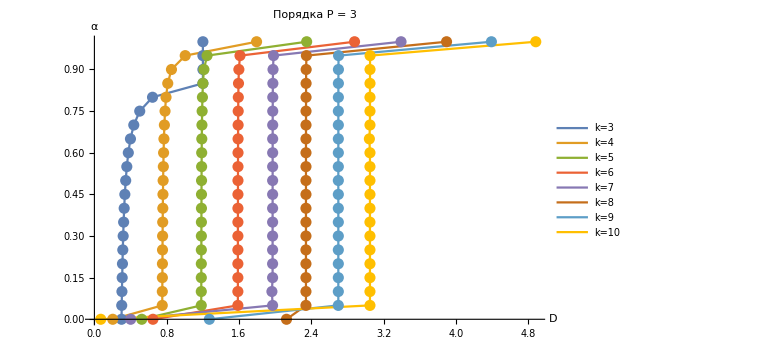

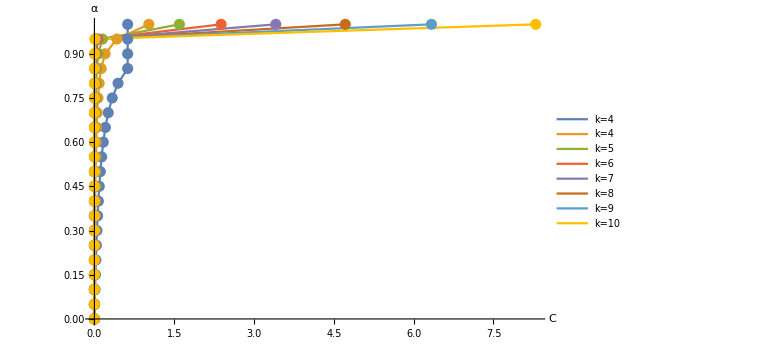

```mathematica
datak3to10o3={{{0.,0.3000000000000002,0.},{0.05,0.30212014134275633,0.00584795321636969},{0.1,0.30452839206740345,0.012392189516776378},{0.15000000000000002,0.3072504373340138,0.01966529635862695},{0.2,0.31036907100100136,0.027840988228984273},{0.25,0.313982596966661,0.03711116132315582},{0.30000000000000004,0.31818181818181834,0.047619047619043856},{0.35000000000000003,0.3232044198895023,0.05982905982906205},{0.4,0.3292682926829268,0.0740740740740738},{0.45,0.33673469387755056,0.09090909090908744},{0.5,0.3461538461538458,0.11111111111111444},{0.55,0.3584070796460175,0.13580246913580155},{0.6000000000000001,0.37499999999999933,0.1666666666666632},{0.65,0.39873415429208886,0.20634911413136572},{0.7000000000000001,0.43548387096774255,0.25925925925925947},{0.75,0.5013393045207973,0.33467122787970005},{0.8,0.642857142857144,0.44444444444444875},{0.8500000000000001,1.1999961059575641,0.6250016091791286},{0.9,1.2000003110933224,0.62500195520447},{0.9500000000000001,1.2000003288367298,0.6250016072525675},{1.,1.2000006401436634,0.6250024214678709}},{{0.,0.2027078880198433,-1.6579330501068986*^-14},{0.05,0.7505298169636501,0.0011768294735858833},{0.1,0.7511195854981662,0.002484862010151783},{0.15000000000000002,0.7517827296749101,0.003952412181121188},{0.2,0.7525083612040134,0.00555555555555524},{0.25,0.7533556185290623,0.007423767493515735},{0.30000000000000004,0.754313600318075,0.00953131359861932},{0.35000000000000003,0.7554278001059133,0.01197519919380359},{0.4,0.75672645699543,0.014814812996410371},{0.45,0.7582520805249889,0.018138553179430993},{0.5,0.7601351351350997,0.022222222221965182},{0.55,0.7624205233160531,0.027151676809741798},{0.6000000000000001,0.7653047751804656,0.033330649197722564},{0.65,0.7690458403351338,0.04127608699265768},{0.7000000000000001,0.7740882600603682,0.05186399224560983},{0.75,0.7812652816061348,0.06669824160809885},{0.8,0.7922538145641428,0.0888898349466369},{0.8500000000000001,0.8113114187838237,0.12595146750478856},{0.9,0.8523090293737319,0.2000628235179059},{0.9500000000000001,1.0044642857142856,0.42222222222221467},{1.,1.7937794390698454,1.0228261425987122}},{{0.,0.5236075621866705,-6.631732200427602*^-14},{0.05,1.182069454863532,0.0004289715751705594},{0.1,1.1822613071410588,0.0009078546939538981},{0.15000000000000002,1.1824738004648525,0.0014380086566111072},{0.2,1.1826983222893546,0.001994354714568659},{0.25,1.1829654236728429,0.002659034795073012},{0.30000000000000004,1.183270851186573,0.003418893796393263},{0.35000000000000003,1.1836234522577282,0.004295533231385208},{0.4,1.1840622035219377,0.005387408593984825},{0.45,1.1845513032574149,0.006601856890341649},{0.5,1.1851395541334502,0.008061144284160564},{0.55,1.1858599858655772,0.009846292411050207},{0.6000000000000001,1.1867577702190821,0.012067861332108501},{0.65,1.18787111501856,0.014815206451070621},{0.7000000000000001,1.1894574137098497,0.018725225578047375},{0.75,1.1915771603793968,0.023932256564956834},{0.8,1.194887521546648,0.03202897573848418},{0.8500000000000001,1.2003689517348937,0.04533617089019038},{0.9,1.211467247796538,0.07191081807141589},{0.9500000000000001,1.2460454514229802,0.15167216555900614},{1.,2.347826760223212,1.5973201856576134}},{{0.,0.6474376779748668,-3.789561257387198*^-14},{0.05,1.5868663644160113,0.00019694137405205453},{0.1,1.586945046245709,0.000427417900311866},{0.15000000000000002,1.5870272789582742,0.000674257545928943},{0.2,1.5871206213780653,0.0009551737224076833},{0.25,1.5872255775204591,0.0012701235573899794},{0.30000000000000004,1.587344471560083,0.0016270858738494094},{0.35000000000000003,1.5874647985990322,0.001982171906433905},{0.4,1.5876424745672753,0.0025163486946553344},{0.45,1.5878312640131658,0.0030809907354599378},{0.5,1.5880324047880088,0.003681176402854666},{0.55,1.5883344856625663,0.0045871638727893104},{0.6000000000000001,1.5886767215311635,0.005610791551646344},{0.65,1.5891220381698694,0.006941905963808873},{0.7000000000000001,1.5897092777960438,0.008696172277353753},{0.75,1.5905317359583526,0.011150972426908847},{0.8,1.591731761739667,0.014724703382872423},{0.8500000000000001,1.593836151956008,0.02098819140366004},{0.9,1.597973200630358,0.033244960829051706},{0.9500000000000001,1.6104754347845216,0.06990369580247108},{1.,2.8775621014545494,2.380907714991207}},{{0.,0.401216306636445,3.789561257387206*^-14},{0.05,1.9708943935452308,0.00006561322853334174},{0.1,1.9635143681188814,0.00027980284584335396},{0.15000000000000002,1.971007946738485,0.00035511257882111147},{0.2,1.9710587610198425,0.0005540793751113899},{0.25,1.9711065360836748,0.0007080349228279677},{0.30000000000000004,1.971159019941922,0.0008884784006113473},{0.35000000000000003,1.9711761764975348,0.0009732872322463968},{0.4,1.971286893784058,0.0013546361640616544},{0.45,1.9713883177431015,0.0017248373237919168},{0.5,1.9714554390498726,0.0019627556524331653},{0.55,1.971616644255278,0.002555581803846963},{0.6000000000000001,1.9717662304314774,0.003128094055625752},{0.65,1.9719453567166707,0.0037568098021836267},{0.7000000000000001,1.9722038133981303,0.004697831838617123},{0.75,1.9725603719843274,0.005995867323955887},{0.8,1.9731130177821083,0.008034926672166879},{0.8500000000000001,1.9740040656527746,0.011244762274192988},{0.9,1.9757455914271616,0.017600717713861517},{0.9500000000000001,1.9811801674942122,0.03721383075917591},{1.,3.391696035134426,3.408760850093851}},{{0.,2.1248571519920505,-3.7895612573872014*^-14},{0.05,2.3399971618748103,0.000060561609984688416},{0.1,2.3400124501246258,0.00012794684329264785},{0.15000000000000002,2.3400295341759247,0.00020320403562360903},{0.2,2.3400487546633757,0.0002878815197012348},{0.25,2.3400705379128475,0.00038384202624304947},{0.30000000000000004,2.340105324261078,0.000557419521915866},{0.35000000000000003,2.3401373345677596,0.000701369916669137},{0.4,2.340157674965798,0.0007676840380289223},{0.45,2.3401972847050696,0.0009421543156425585},{0.5,2.3402448185028883,0.0011515259327173533},{0.55,2.340302917548371,0.0014074150491296675},{0.6000000000000001,2.3403755459775852,0.0017272887538410941},{0.65,2.340468931711355,0.0021385484319201473},{0.7000000000000001,2.340593457455839,0.0026868913217109984},{0.75,2.3407678160932246,0.0034545782361495476},{0.8,2.3410506591539733,0.00471358941734934},{0.8500000000000001,2.3414904619073913,0.00665018959481737},{0.9,2.3423304800783393,0.010345999398604519},{0.9500000000000001,2.3449602271438175,0.021878995321894013},{1.,3.8952931237929804,4.714589437104338}},{{0.,1.2714265657708095,-5.684341886080802*^-14},{0.05,2.6980943215731106,0.00003808558663346651},{0.1,2.698102344919196,0.00008035746518923285},{0.15000000000000002,2.6981112908841345,0.00012704912512617741},{0.2,2.6981214064759746,0.00018090644653057097},{0.25,2.698132842152914,0.0002411998076847036},{0.30000000000000004,2.698145911582383,0.0003101058736471409},{0.35000000000000003,2.6981609733354652,0.0003891310869524506},{0.4,2.6981785795999724,0.00048221065753750736},{0.45,2.6982173201712865,0.0009180471620311432},{0.5,2.6982243340840273,0.0007236261696637786},{0.55,2.69825483261626,0.0008844308465919922},{0.6000000000000001,2.698299140056113,0.0011817339075908728},{0.65,2.698369091797204,0.0015737496368046777},{0.7000000000000001,2.698394324699899,0.0016722852333259652},{0.75,2.6985124048158644,0.002334154969124332},{0.8,2.698639255288224,0.003009987125911569},{0.8500000000000001,2.698854512399266,0.004125182291356094},{0.9,2.6992785728680175,0.006624198302612662},{0.9500000000000001,2.7006969529842673,0.013748853751489298},{1.,4.3914896648497015,6.333483249100823}},{{0.,0.07024141784204734,7.579122514774464*^-13},{0.05,3.0480421928055565,0.00002520191261131305},{0.1,3.0480466816840126,0.00005322731359077198},{0.15000000000000002,3.048051698279502,0.00008453747913487561},{0.2,3.048057341379524,0.00011974332922667001},{0.25,3.0480637381782425,0.00015968194297026145},{0.30000000000000004,3.0480710319981186,0.0002048088585979714},{0.35000000000000003,3.047843214243828,0.002194966137418912},{0.4,3.0480892082299373,0.00031582839771241783},{0.45,3.048100951822584,0.00039190985035020276},{0.5,3.0481149086658443,0.00047904148376195116},{0.55,3.0481319452613764,0.0005848555714464966},{0.6000000000000001,3.0481532861721767,0.0007185150125602983},{0.65,3.041606081017998,0.0008272785872425935},{0.7000000000000001,3.0482172550601248,0.0011177687738002833},{0.75,3.048268430830856,0.0014371322908649136},{0.8,3.0482382927496863,0.0019112581943924547},{0.8500000000000001,3.048473137859323,0.002714173511966084},{0.9,3.0487290857889286,0.004311269066003358},{0.9500000000000001,3.049497165496931,0.009101870744871118},{1.,4.882240245278928,8.294476864910012}}};k3to10Do3=ListLinePlot[Table[datak3to10o3[[x,All,{2,1}]],{x,1,8}],Joined->True,PlotLegends->{"k=3","k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[D],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 3",18]]
k3to10Co3=ListLinePlot[Table[datak3to10o3[[x,All,{3,1}]],{x,1,8}],Joined->True,PlotLegends->{"k=4","k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[C],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All]
```

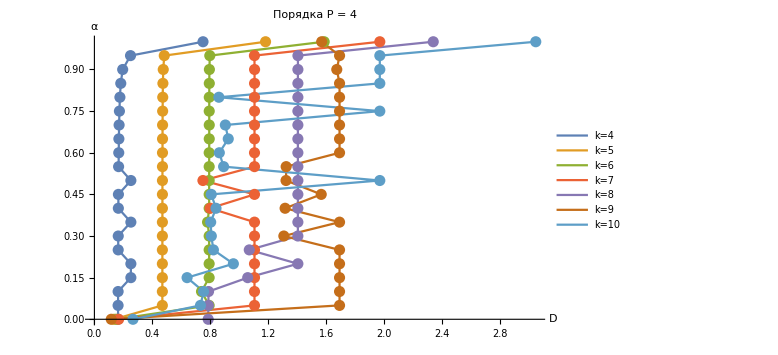

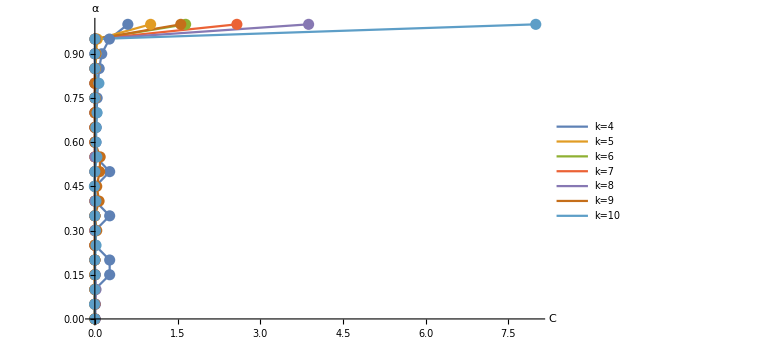

```mathematica
datak4to10o4={{{0.,0.16333938293578398,-1.0636540537234382*^-10},{0.05,0.16349555406826605,0.0007309941520778321},{0.1,0.16366942816730357,0.0015432098764828542},{0.15000000000000002,0.25180989439016166,0.26888544090329175},{0.2,0.25180986756647916,0.268884611923344},{0.25,0.16433353624315544,0.004629628764390235},{0.30000000000000004,0.16461980672045018,0.005952375999455265},{0.35000000000000003,0.2518093319178751,0.26887044033340585},{0.4,0.16533986527864172,0.009259259258904712},{0.45,0.1658013732591581,0.011363634589429183},{0.5,0.2518093319077909,0.2688704400780698},{0.55,0.16704475147181191,0.016975304950813112},{0.6000000000000001,0.1681115908318286,0.021729579180218266},{0.65,0.16903675878722277,0.025793650793506574},{0.7000000000000001,0.1705622236260248,0.0324074074073943},{0.75,0.17274472168908148,0.04166666666529495},{0.8,0.17612524461833812,0.05555555555384896},{0.8500000000000001,0.1820633850292958,0.07870370367984778},{0.9,0.19522776572663822,0.12499999999949961},{0.9500000000000001,0.24930747922437746,0.2638888888888385},{1.,0.7499999951846595,0.5986110180315942}},{{0.,0.13634647645544895,-3.384381367747355*^-9},{0.05,0.46919301237956784,0.0001218311420492078},{0.1,0.4692327497412121,0.0002572015911406797},{0.15000000000000002,0.4692771698881243,0.00040849109415527643},{0.2,0.46932715288802895,0.0005787034773372095},{0.25,0.4693838130166025,0.0007716048338352261},{0.30000000000000004,0.46944856627663817,0.0009913296072985153},{0.35000000000000003,0.4695233423997807,0.0012464387463751348},{0.4,0.46961059039520653,0.0015432098765510707},{0.45,0.46971374347619965,0.001893939394032414},{0.5,0.4698375870069186,0.002314814812863612},{0.55,0.46998904003602704,0.0028292181040569637},{0.6000000000000001,0.4701784936874088,0.0034722222216866327},{0.65,0.4704223008215474,0.004298914117513646},{0.7000000000000001,0.4707477707760339,0.005401178239829586},{0.75,0.4712041878529075,0.0069444166087578255},{0.8,0.4718904745206215,0.009259246154852015},{0.8500000000000001,0.47303873852123235,0.013117282141517235},{0.9,0.475352112604836,0.020833330679026072},{0.9500000000000001,0.4824300178677719,0.043981481481379606},{1.,1.1819003535851251,1.0120779542433262}},{{0.,0.15163493018270124,1.0610771520684184*^-13},{0.05,0.7923719933718761,0.00003808117106321635},{0.1,0.7396461468383556,0.002534634546661132},{0.15000000000000002,0.7923954399415551,0.00012768346784165855},{0.2,0.7924093620175602,0.00018088570686813907},{0.25,0.7924251409481772,0.00024118094200578844},{0.30000000000000004,0.7924431747812455,0.0003100897830487766},{0.35000000000000003,0.7813291518054468,0.0008668152562525691},{0.4,0.7924882629482715,0.0004823615529403472},{0.45,0.7925169580930641,0.0005919892045312729},{0.5,0.7925513930810181,0.0007234557386254896},{0.55,0.7925934886497541,0.000884330100446581},{0.6000000000000001,0.7926461119772552,0.0010853142395869037},{0.65,0.7930621230623679,0.003049148149572525},{0.7000000000000001,0.7931747844838068,0.003430067609269825},{0.75,0.7929303987345957,0.0021706284833726388},{0.8,0.7933232427188128,0.005101139989437793},{0.8500000000000001,0.7934363012456023,0.004100075988223275},{0.9,0.7940695879127079,0.006511885449981493},{0.9500000000000001,0.7967940307783085,0.01722299174396843},{1.,1.5868031038970365,1.6470689581074862}},{{0.,0.1670803600572845,-7.124375163887963*^-13},{0.05,1.105501790835376,0.00001567384858086976},{0.1,1.1055054434722296,0.00003309661724415492},{0.15000000000000002,1.1055095257891663,0.00005256521706845285},{0.2,1.105514118431793,0.00007446739361209144},{0.25,1.1055193234728617,0.00009928985808376934},{0.30000000000000004,1.1055252721511881,0.00012765838600898856},{0.35000000000000003,1.1055321343542992,0.00016029288960150257},{0.4,0.7990315551063571,0.002544665525965684},{0.45,1.1055496083202239,0.00024371146352374743},{0.5,0.749414756652653,0.003884058701684502},{0.55,1.1055748469607989,0.0003640628140904787},{0.6000000000000001,1.1055921991945554,0.0004468043622182445},{0.65,1.1056145098092491,0.0005531752103706827},{0.7000000000000001,1.1056442591537508,0.0006950284476564168},{0.75,1.1056859106269732,0.0008936063189442697},{0.8,1.1057483937204378,0.0011914731353044764},{0.8500000000000001,1.1058525480682522,0.0016879269380448618},{0.9,1.1060609154096666,0.002680821496854456},{0.9500000000000001,1.1050499883001694,0.011432923234876085},{1.,1.9709239389287658,2.5771624526139614}},{{0.,0.7857638542109887,0.009038946176284906},{0.05,0.7869520993290132,0.011031800959244727},{0.1,0.7882533093449053,0.02109645150142872},{0.15000000000000002,1.0587056413742713,0.008960344569338002},{0.2,1.405157008465104,0.00003598518578655784},{0.25,1.0695392530555983,0.0029873495395804626},{0.30000000000000004,1.4051612162453724,0.00006168889691859171},{0.35000000000000003,1.4051638056599132,0.00007750648119326793},{0.4,1.4051668266023025,0.00009595662971454055},{0.45,1.4051703969440963,0.00011776970447196312},{0.5,1.4051746813113848,0.000143940759699035},{0.55,1.405179917187979,0.0001758853959472618},{0.6000000000000001,1.4051864634558335,0.0002159111392150711},{0.65,1.405194879394288,0.00026731855417286483},{0.7000000000000001,1.4052061006819216,0.0003358536005786543},{0.75,1.4052218110141548,0.0004318177208915583},{0.8,1.4052453771414135,0.0005757629994756529},{0.8500000000000001,1.4052846552917755,0.0008156389722595725},{0.9,1.4053632193342072,0.0012954667457961476},{0.9500000000000001,1.4055989630251475,0.0027348744305830527},{1.,2.3399834073481913,3.8788326272753104}},{{0.,0.11633472832424513,-3.6379788070916834*^-13},{0.05,1.692885569148113,4.0736907976679524*^-6},{0.1,1.6928861474637809,8.600002911407503*^-6},{0.15000000000000002,1.6928867938093066,0.00001365814162757791},{0.2,1.6928875209038279,0.000019344572016658873},{0.25,1.6928883450459822,0.000025798132022221876},{0.30000000000000004,1.3081587932147412,0.03432565595467166},{0.35000000000000003,1.6928903735779632,0.00004167243793441838},{0.4,1.3169491192944953,0.07658575501445737},{0.45,1.5664121998142395,0.03428836666498679},{0.5,1.3233630528527434,0.08720758582136716},{0.55,1.3242959671698706,0.09645978290888403},{0.6000000000000001,1.6928998825799149,0.00011610017306035537},{0.65,1.6929034145030146,0.00014374307963104597},{0.7000000000000001,1.692908123754387,0.0001806000809059088},{0.75,1.6929147167558922,0.0002322003743150466},{0.8,1.692924606349801,0.0003096003991837887},{0.8500000000000001,1.6929410892659138,0.00043860070800292314},{0.9,1.6738047932011668,0.012480735734364623},{0.9500000000000001,1.6930729641417235,0.0014706023441855612},{1.,1.569491014498845,1.5589714799208503}},{{0.,0.26629625933259066,2.1827872842550285*^-12},{0.05,0.7325948291000843,-0.005629087632041777},{0.1,0.7538139359857052,0.002005360748201686},{0.15000000000000002,0.6400083010967453,0.004265489846147825},{0.2,0.9596987462112213,0.000010939259906687475},{0.25,0.8217957231559966,0.02130681708980166},{0.30000000000000004,0.8074383355926461,0.012290853333191383},{0.35000000000000003,0.8030070205299275,-0.0009138685575332298},{0.4,0.8397375738505061,0.019724219582712966},{0.45,0.806942984086225,-0.008038888392547955},{0.5,1.9709294040237209,0.0000449602954176953},{0.55,0.8921558440130989,0.03683620395392302},{0.6000000000000001,0.8626127887675501,0.017915709969141373},{0.65,0.9243838294242303,0.018378944555418768},{0.7000000000000001,0.9042760940958525,0.03997471251107829},{0.75,1.9709384499889735,0.0001348808828576391},{0.8,0.8595378969448538,0.07347885233187591},{0.8500000000000001,1.9709505114051598,0.0002547749914810992},{0.9,1.9709655883832191,0.0004046426564552044},{0.9500000000000001,1.9710108206976917,0.0008542452307059045},{1.,3.048038153507523,8.000924606009113}}};
k4to10Do4=ListLinePlot[Table[datak4to10o4[[x,All,{2,1}]],{x,1,7}],Joined->True,PlotLegends->{"k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[D],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 4",18]]
k4to10Co4=ListLinePlot[Table[datak4to10o4[[x,All,{3,1}]],{x,1,7}],Joined->True,PlotLegends->{"k=4","k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[C],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All]
```

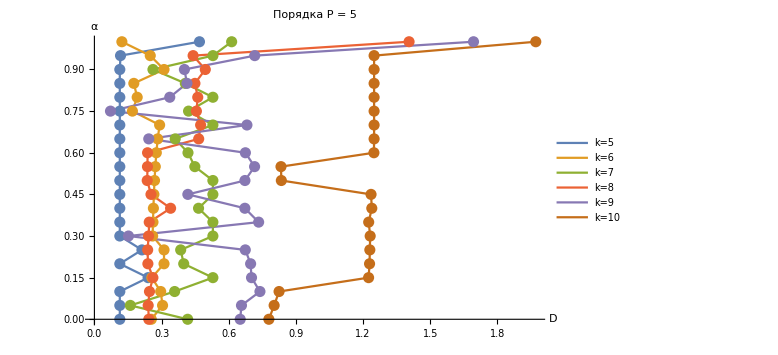

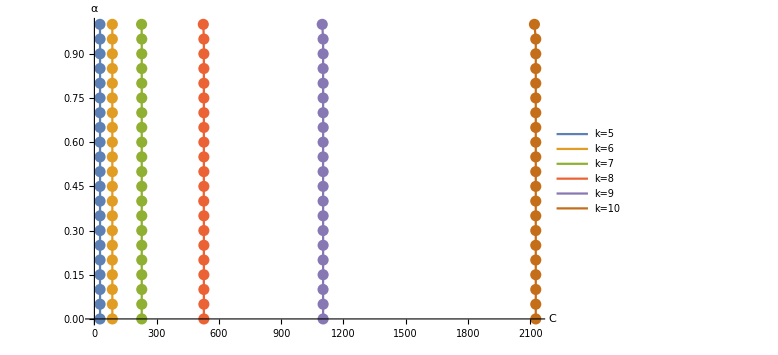

```mathematica
datak5to10o5={{{0.,0.11343533945922266,27.230151168902264},{0.05,0.11343165647909244,27.230173487802308},{0.1,0.11343353212801212,27.230177448381973},{0.15000000000000002,0.23974103766909424,26.939229460190816},{0.2,0.11342968858350301,27.230168796537253},{0.25,0.21226316319981897,26.973590630383907},{0.30000000000000004,0.113445910491092,27.230130970323895},{0.35000000000000003,0.11343652073453814,27.230168798349972},{0.4,0.11343442536706765,27.230183582819134},{0.45,0.11342968858260913,27.230168796580323},{0.5,0.11343398728963996,27.2301731281148},{0.55,0.11343430837458175,27.230170708979337},{0.6000000000000001,0.1134361534851122,27.230177556880015},{0.65,0.113429688584434,27.230168796532425},{0.7000000000000001,0.11342948490418991,27.23017830771576},{0.75,0.11367561442890098,27.228978855586274},{0.8,0.11343605094656731,27.230176276123352},{0.8500000000000001,0.11342968684376814,27.23016880588827},{0.9,0.11342968858443511,27.230168796532165},{0.9500000000000001,0.11657816418050458,27.215236755157946},{1.,0.4691572528843008,26.812384261087416}},{{0.,0.2540383122570742,86.39925553854235},{0.05,0.30431771933835994,86.39862699422459},{0.1,0.29593982183965867,86.39892113636154},{0.15000000000000002,0.256433994089308,86.399253359592},{0.2,0.3108260427050423,86.39854262755769},{0.25,0.3108689828885101,86.39853984715697},{0.30000000000000004,0.2599617785555634,86.39924261483026},{0.35000000000000003,0.2615395868960923,86.399235088522},{0.4,0.2634120137057469,86.39922410448686},{0.45,0.2656698681616541,86.39920804085067},{0.5,0.268445445032692,86.39918431849922},{0.55,0.27193918900752007,86.39914867342524},{0.6000000000000001,0.2764699326203547,86.39909371400358},{0.65,0.2825767709522622,86.39900585462267},{0.7000000000000001,0.2912478613784835,86.39885819690193},{0.75,0.16972674518527475,86.17805601830058},{0.8,0.19102101403349991,86.39626851160938},{0.8500000000000001,0.1760083518145419,86.39367380275085},{0.9,0.31083933168737443,86.39845176218186},{0.9500000000000001,0.24940810221805768,86.39535949865032},{1.,0.12265866023909736,86.31022717142788}},{{0.,0.4163866092805613,228.20277777777264},{0.05,0.1603596891942936,228.20216550664847},{0.1,0.35825406088596873,228.20282730878375},{0.15000000000000002,0.529073667829465,228.20277001975907},{0.2,0.3988122957216667,228.20270046088302},{0.25,0.3852373521590839,228.2025301561705},{0.30000000000000004,0.529075626842534,228.20275893714577},{0.35000000000000003,0.5290764882288399,228.2027541057431},{0.4,0.46501679193688195,228.20267690719407},{0.45,0.5290786674428546,228.20274180856896},{0.5,0.5290800789139259,228.20273381557416},{0.55,0.4484349892797917,228.18578154933297},{0.6000000000000001,0.4178907398330255,228.202997359987},{0.65,0.3608157502294049,228.1664423628878},{0.7000000000000001,0.5290904684634274,228.2026751993647},{0.75,0.4204450248374283,228.20332519397596},{0.8,0.529103456546158,228.20260192831176},{0.8500000000000001,0.40604592703539827,228.19868741670263},{0.9,0.2614363682049134,228.17902244458702},{0.9500000000000001,0.529220350759957,228.20194249281346},{1.,0.6128633040672681,227.32795392570233}},{{0.,0.2428928242406916,527.491666798819},{0.05,0.2401137741365175,527.4916067903753},{0.1,0.24591333185703576,527.4900160966644},{0.15000000000000002,0.2612027710518094,527.491782841112},{0.2,0.2388056963097867,527.4913174388264},{0.25,0.23782853217766786,527.4951735822655},{0.30000000000000004,0.24192308957234065,527.4911845448529},{0.35000000000000003,0.24484777775857358,527.4906100189937},{0.4,0.3402010196121479,526.9036665351101},{0.45,0.25264167866751136,527.4413418929947},{0.5,0.2358358272985574,527.4886755397329},{0.55,0.23699852258570817,527.486369763687},{0.6000000000000001,0.23736557727503152,527.4915431510789},{0.65,0.4657283688281552,527.4866706230167},{0.7000000000000001,0.47429574881763403,527.4872685325671},{0.75,0.4554710213337841,527.492011521748},{0.8,0.4614834405235749,527.4912501374331},{0.8500000000000001,0.44885030211331645,527.4912219554617},{0.9,0.4951621748589012,527.4924901451323},{0.9500000000000001,0.44080072800641357,527.4881318488962},{1.,1.4051507651699595,524.7681209314442}},{{0.,0.6510493598532128,1102.2027777777755},{0.05,0.6567154096253874,1102.2027771071985},{0.1,0.7392110642183403,1101.8914144833157},{0.15000000000000002,0.7016169630494946,1102.2033011372073},{0.2,0.6975461473602307,1102.2027756135478},{0.25,0.6737700015743887,1102.2027719243536},{0.30000000000000004,0.15211195955064385,1102.2028884838226},{0.35000000000000003,0.7333804104317632,1102.202774196356},{0.4,0.6719186102082099,1102.2027608412116},{0.45,0.4172668444827832,1102.1479485428163},{0.5,0.6722229602693286,1102.2027646804265},{0.55,0.715259779546717,1102.0351290097728},{0.6000000000000001,0.6742558247044248,1102.2027515507166},{0.65,0.24272137908827982,1102.479164223985},{0.7000000000000001,0.6811231804926343,1102.2027502010978},{0.75,0.07178754210632403,1102.2022258291247},{0.8,0.3364648705039829,1102.1866218760008},{0.8500000000000001,0.41333225706845117,1102.1510733234404},{0.9,0.4018911216294296,1102.1823281673644},{0.9500000000000001,0.7159532102776226,1102.2025512899932},{1.,1.6928850486190248,1097.941225066692}},{{0.,0.7790786350900087,2127.002777783576},{0.05,0.8025520031740389,2127.00277770443},{0.1,0.824606109318358,2127.0027781801605},{0.15000000000000002,1.2243624865741658,2127.002777831337},{0.2,1.2286761851030044,2127.0027779685906},{0.25,1.2299095544022487,2127.0027778467393},{0.30000000000000004,1.2314506984306506,2127.0027774934883},{0.35000000000000003,1.2248182540353547,2127.002778026657},{0.4,1.238680870935531,2127.002779915334},{0.45,1.2353369569145918,2127.0027786840164},{0.5,0.8347556114710728,2127.0124076583634},{0.55,0.8331974577933793,2127.008509179639},{0.6000000000000001,1.2481752824800627,2127.0027760690195},{0.65,1.248968991917978,2127.002771098003},{0.7000000000000001,1.2489687652482102,2127.0027692583317},{0.75,1.248968820808976,2127.002766823767},{0.8,1.2489693263392865,2127.002763301801},{0.8500000000000001,1.248970094408235,2127.002757395126},{0.9,1.2489706323531748,2127.0027453130033},{0.9500000000000001,1.2489732373274227,2127.002709323824},{1.,1.970924881037972,2120.5391021320065}}};
k5to10Do5=ListLinePlot[Table[datak5to10o5[[x,All,{2,1}]],{x,1,6}],Joined->True,PlotLegends->{"k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[D],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 5",18]]
k5to10Co5=ListLinePlot[Table[datak5to10o5[[x,All,{3,1}]],{x,1,6}],Joined->True,PlotLegends->{"k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[C],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All]
```

```mathematica
datak1to10o1[[1]]
```

{{0.,1.,1.},{0.05,1.05556,0.947368},{0.1,1.125,0.888889},{0.15,1.21429,0.823529},{0.2,1.33333,0.75},{0.25,1.5,0.666667},{0.3,1.75,0.571429},{0.35,2.16667,0.461538},{0.4,3.,0.333333},{0.45,4.,0.25},{0.5,4.,0.25},{0.55,4.,0.25},{0.6,4.,0.25},{0.65,4.,0.25},{0.7,4.,0.25},{0.75,4.,0.25},{0.8,4.,0.25},{0.85,4.,0.25},{0.9,4.,0.25},{0.95,4.,0.25},{1.,4.,0.25}}

```mathematica
datak1to10o1[[2]]
```

{{0.,1.99942,3.},{0.05,2.02367,2.98246},{0.1,2.05063,2.96296},{0.15,2.08163,2.94118},{0.2,2.11765,2.91667},{0.25,2.16,2.88889},{0.3,2.21053,2.85714},{0.35,2.27184,2.82051},{0.4,2.34783,2.77778},{0.45,2.44444,2.72727},{0.5,2.57143,2.66667},{0.55,2.74576,2.59259},{0.6,3.,2.5},{0.65,3.40541,2.38095},{0.7,4.15385,2.22222},{0.75,5.4047,2.05486},{0.8,5.64774,2.0264},{0.85,5.81879,2.00163},{0.9,5.92692,1.98003},{0.95,5.9835,1.9611},{1.,6.,1.94444}}

```mathematica
bs=Sum[r[s]^2,{s,0,2}];
k=bs
```

r[0]^2+r[1]^2+r[2]^2

```mathematica
Remove[α,OptimCod,k,o,R,f,bs,con,cons,β];
k=3;o=3;t=0;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];

p=(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,4,4}])^2;

OptimCod=t*bs+(1-t)*p;
OptimCod[[1]]
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{OptimCod[[1]],cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
sol[[2]];
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b];
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
Constanterror=Subscript[C, o+1]/σ[1];
{t,-Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π,Subscript[C, o+1]/σ[1]}
```

(1/4+r[0] r[1]+9 r[0] r[2]+r[1] r[2]+35 r[0] r[3]+9 r[1] r[3]+r[2] r[3])^2

{0,0.3,4.0833333333333333333333333333333333333333333333}

```mathematica
datak3to10o3
```

{{{0.,0.3,4.08333},{0.05,0.30212,4.07749},{0.1,0.304528,4.07094},{0.15,0.30725,4.06367},{0.2,0.310369,4.05549},{0.25,0.313983,4.04622},{0.3,0.318182,4.03571},{0.35,0.323204,4.0235},{0.4,0.329268,4.00926},{0.45,0.336735,3.99242},{0.5,0.346154,3.97222},{0.55,0.358407,3.94753},{0.6,0.375,3.91667},{0.65,0.398734,3.87698},{0.7,0.435484,3.82407},{0.75,0.501339,3.74866},{0.8,0.642857,3.63889},{0.85,1.2,3.45833},{0.9,1.2,3.45833},{0.95,1.2,3.45833},{1.,1.2,3.45833}},{{0.,0.202708,14.0833},{0.05,0.75053,14.0822},{0.1,0.75112,14.0808},{0.15,0.751783,14.0794},{0.2,0.752508,14.0778},{0.25,0.753356,14.0759},{0.3,0.754314,14.0738},{0.35,0.755428,14.0714},{0.4,0.756726,14.0685},{0.45,0.758252,14.0652},{0.5,0.760135,14.0611},{0.55,0.762421,14.0562},{0.6,0.765305,14.05},{0.65,0.769046,14.0421},{0.7,0.774088,14.0315},{0.75,0.781265,14.0166},{0.8,0.792254,13.9944},{0.85,0.811311,13.9574},{0.9,0.852309,13.8833},{0.95,1.00446,13.6611},{1.,1.79378,13.0605}},{{0.,0.523608,36.75},{0.05,1.18207,36.7496},{0.1,1.18226,36.7491},{0.15,1.18247,36.7486},{0.2,1.1827,36.748},{0.25,1.18297,36.7473},{0.3,1.18327,36.7466},{0.35,1.18362,36.7457},{0.4,1.18406,36.7446},{0.45,1.18455,36.7434},{0.5,1.18514,36.7419},{0.55,1.18586,36.7402},{0.6,1.18676,36.7379},{0.65,1.18787,36.7352},{0.7,1.18946,36.7313},{0.75,1.19158,36.7261},{0.8,1.19489,36.718},{0.85,1.20037,36.7047},{0.9,1.21147,36.6781},{0.95,1.24605,36.5983},{1.,2.34783,35.1527}},{{0.,0.647438,80.0833},{0.05,1.58687,80.0831},{0.1,1.58695,80.0829},{0.15,1.58703,80.0827},{0.2,1.58712,80.0824},{0.25,1.58723,80.0821},{0.3,1.58734,80.0817},{0.35,1.58746,80.0814},{0.4,1.58764,80.0808},{0.45,1.58783,80.0803},{0.5,1.58803,80.0797},{0.55,1.58833,80.0787},{0.6,1.58868,80.0777},{0.65,1.58912,80.0764},{0.7,1.58971,80.0746},{0.75,1.59053,80.0722},{0.8,1.59173,80.0686},{0.85,1.59384,80.0624},{0.9,1.59797,80.0501},{0.95,1.61048,80.0134},{1.,2.87756,77.7025}},{{0.,0.401216,154.083},{0.05,1.97089,154.083},{0.1,1.96351,154.083},{0.15,1.97101,154.083},{0.2,1.97106,154.083},{0.25,1.97111,154.083},{0.3,1.97116,154.082},{0.35,1.97118,154.082},{0.4,1.97129,154.082},{0.45,1.97139,154.082},{0.5,1.97146,154.081},{0.55,1.97162,154.081},{0.6,1.97177,154.08},{0.65,1.97195,154.08},{0.7,1.9722,154.079},{0.75,1.97256,154.077},{0.8,1.97311,154.075},{0.85,1.974,154.072},{0.9,1.97575,154.066},{0.95,1.98118,154.046},{1.,3.3917,150.675}},{{0.,2.12486,270.75},{0.05,2.34,270.75},{0.1,2.34001,270.75},{0.15,2.34003,270.75},{0.2,2.34005,270.75},{0.25,2.34007,270.75},{0.3,2.34011,270.749},{0.35,2.34014,270.749},{0.4,2.34016,270.749},{0.45,2.3402,270.749},{0.5,2.34024,270.749},{0.55,2.3403,270.749},{0.6,2.34038,270.748},{0.65,2.34047,270.748},{0.7,2.34059,270.747},{0.75,2.34077,270.747},{0.8,2.34105,270.745},{0.85,2.34149,270.743},{0.9,2.34233,270.74},{0.95,2.34496,270.728},{1.,3.89529,266.035}},{{0.,1.27143,444.083},{0.05,2.69809,444.083},{0.1,2.6981,444.083},{0.15,2.69811,444.083},{0.2,2.69812,444.083},{0.25,2.69813,444.083},{0.3,2.69815,444.083},{0.35,2.69816,444.083},{0.4,2.69818,444.083},{0.45,2.69822,444.083},{0.5,2.69822,444.083},{0.55,2.69825,444.082},{0.6,2.6983,444.082},{0.65,2.69837,444.082},{0.7,2.69839,444.082},{0.75,2.69851,444.081},{0.8,2.69864,444.08},{0.85,2.69885,444.079},{0.9,2.69928,444.077},{0.95,2.7007,444.07},{1.,4.39149,437.75}},{{0.,0.0702414,690.083},{0.05,3.04804,690.083},{0.1,3.04805,690.083},{0.15,3.04805,690.083},{0.2,3.04806,690.083},{0.25,3.04806,690.083},{0.3,3.04807,690.083},{0.35,3.04784,690.082},{0.4,3.04809,690.083},{0.45,3.0481,690.083},{0.5,3.04811,690.083},{0.55,3.04813,690.083},{0.6,3.04815,690.083},{0.65,3.04161,690.083},{0.7,3.04822,690.082},{0.75,3.04827,690.082},{0.8,3.04824,690.081},{0.85,3.04847,690.081},{0.9,3.04873,690.079},{0.95,3.0495,690.074},{1.,4.88224,681.789}}}

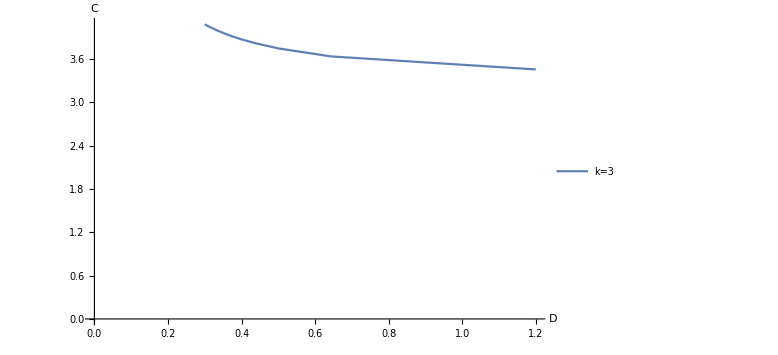

```mathematica
ListLinePlot[Table[datak3to10o3[[x,All,{2,3}]],{x,1,1}],Joined->True,PlotLegends->{"k=3"},AxesLabel->{HoldForm[D],HoldForm[C]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.}]
```

```mathematica
data4interl500={{{0.,0.27245401075856860477716526739250817139983547865460123273036771710525208311217`47.914847741153736,34.5666666666666666666666666666666666666666667544387460695542`47.03343850629213},{0.05,0.46919301240815828786073431068932170999458630142564149843152303136883224825889`48.3558148973091,34.5667884990253411306167467572913077359480106507585958549862`47.696731221847},{0.1,0.46923274974253347065114426440861518158916424683705803830962157481698120398478`48.35583769621424,34.5669238683127572016540225124644572796141448617868617586538`47.69679284605789},{0.15000000000000002,0.49789231244633455980615142622880768481563652055471959133138532036778408881195`48.050547112110095,34.5798935532029065170334079920251063237636508325618392076902`47.433292537283904},{0.2,0.48472806412094719963975994458888186408541222972869245752989376146579956073202`47.999795554157494,34.586141699202414118184336425914911686688185702586044601443`47.37449227499207},{0.25,0.92946466763352402163495731085052586008410635308394715739802700298636154004578`48.08774921091054,34.5671926032179499437449008414194672736895994402523862948835`47.728427311715016},{0.30000000000000004,0.8097017706751152510737812901297446243733884840841212614562964870224312209824`48.2747712507114,34.5932480045014739620858240139384714274373425161325759456641`47.87840601757949},{0.35000000000000003,1.2611842117901783854375850291156002447169890526100823072311`47.681187411071434,34.5689240016023916879036175971235868199850951927493136170524`47.47155333400119},{0.4,1.0994704630268005973620401401974283079265608188592331557185`47.74219182870709,34.5858528029214183322056863469440428881732292390968890964953`47.47792869221766},{0.45,0.85859749016873613252172448944255480506226834700248925055561316308989033440106`47.974636472915805,34.6001060971127837967966594331452701356343362397349914783484`47.58995896821744},{0.5,1.2293434967476833779536630108147222542469477809950367139185`47.66349745967904,34.5928501200193970799376399231063322522355163990066309195146`47.4503695526059},{0.55,0.46998904003610341063239497519883568550745821301441917099262951257415026805402`48.356272940365336,34.5694958847736625519479757771491342706847948249292403032957`47.69796643697558},{0.6000000000000001,1.3448465791556374976749090535603908909626856326295601183059`47.58105935085926,34.5871317844516433029098371603614366565178519814285899282422`47.407471042179424},{0.65,1.3275618334137065308743752463915484300533789971050101870127`47.496375106802816,34.579601878282943478680783654158474333560115668679239004635`47.317432259650346},{0.7000000000000001,0.70861973234899673388445872263082137255527199935331341701949810168259805479347`48.333412775970665,35.0649313047408481206747051337065406457985882089297043643482`47.86548396488544},{0.75,0.71496635294275903794995193711329674581685134433852605169845203849097554510597`48.32616275608941,35.0566348358191774098992974916142042504128033944136935723215`47.86229980604524},{0.8,1.58872215880252174530442725378168118878029029718712346210009212343446772726078`48.23782284942661,34.6005528332042716359056956677398745955494946987341373485114`48.11801588071377},{0.8500000000000001,2.0686520785043151409951693928419311300996073351670900719223`48.07092653942086,34.6024941790991101191370299577676984828616227013841917406832`48.07687448131761},{0.9,1.8383566166175818046879183740644084544356250989161042369045`48.035267085047394,34.5811731530918551455239171557784385717523242454956614984192`47.98423243098302},{0.9500000000000001,2.0171492605493007829563343509735189555628017304797986462321`47.73681210593314,34.6183676923735830198530837118287486801275273190967869795198`47.734900585279455},{1.,0.57387727384590384594587524306504438112108856625850443311617980492977825110322`47.94340493385069,34.9363211122052975238500647370697759302282189647821956945163`47.38078915779049}},{{0.,0.10794551221651338483670250038564787377770194190603096818849527153307531052464`47.83766623989595,90.8333333333333333333333333333333333333333333333333333406166`46.558980046176444},{0.05,0.5109676725426350992970286116023381082764093324255709495788`47.309122767383485,90.7840596758810690753751343866880565535645667828740590047633`46.70021457285106},{0.1,0.5109676725426350992970286116023381082764093324255709495788`47.309122767383485,90.7840596758810690753751343866880565535645667828740590047633`46.70021457285106},{0.15000000000000002,0.5109676725426350992970286116023381082764093324255709495788`47.309122767383485,90.7840596758810690753751343866880565535645667828740590047633`46.70021457285106},{0.2,0.5128522530063462714674105879279797325469760233210540737409`47.38138263407284,90.9602619849486312459378292859073197572950401171172926646816`46.78225189846256},{0.25,0.6038038683728441623819159752726029074136217993681785580757`47.54164267829441,90.8205078182574184043901162000670693003694662650133834345116`47.00731179610359},{0.30000000000000004,0.9017378145342186833903725424029360258384563920823582227898`47.51189595530317,90.8248987851374359929578530908093211022521847799409714323117`47.15846497695321},{0.35000000000000003,0.7924639840701512246255381522107230313362642347459590825937561515674709897767`48.49342974129099,90.8337229333175339842938726700076479490211627056105615172304`48.06996645590743},{0.4,1.1700670109287397218897344393149175203526542806913712674012`48.14014715252235,90.8001505811362746705115765468043346590783264868726651234994`47.89917179668166},{0.45,0.9979450940016396956545919348934369721980040770985404305061`46.97088329976625,90.7768445891622167890395675096883140127266882878469043911279`46.65908416263511},{0.5,0.51131057555121063092774008044050837850549317245261816698315551121355093735693`48.52130737794592,90.7944307875073684393638157392451622668199018454153879427854`47.918175567698555},{0.55,1.4068952044158251117868737018006927825207173444646388524444`47.864925220431815,90.8521773604656876687165684014881623654592673172664468682282`47.70115691543178},{0.6000000000000001,0.7926461119773039743252090257719928555497040454490027662360834032360179394464`48.4934328499293,90.8344186475750351468734730944465509761918147098358274903891`48.0700759844519},{0.65,0.7927137808092017874929697749895324525186444712554082792706505500146600852597`48.36279674585485,90.8346770557278212925883315970875966737341152400501872334966`47.939479414546625},{0.7000000000000001,0.44323643409455854408717533431311906286570066349413732093200775124486820323737`47.760425102500015,90.8881195320153104942531648177101182600596854105458812974064`47.08825533351391},{0.75,1.4621580448073338755520475423429753181444387276462898247467`47.57718832567489,90.8747604493931513411263788653144051060427264353137719405849`47.436713030872895},{0.8,1.5771700830397028231497523353444964269917653077893686993328`46.78628550972728,90.8765163775939738854240681554622929100848818204029017742433`46.68260110910778},{0.8500000000000001,0.33362836515601175486706099178841045437573677889226766525279385150359034448421`48.25155731715833,90.8079271972051126518677114469093657181637635728195209638442`47.455837573805056},{0.9,1.2875413119428570856728051539620785383950787491966779259671`46.46284425603726,90.8456526288794673142331722618090447026751463851817891526817`46.262587050606264},{0.9500000000000001,0.456800491502967030598435325874658644331832520060065930783`47.39254188198428,91.2137855616693475930154043965369394699067836271535246913867`46.73925595440809},{1.,1.58680310399564246571081876894727390321252184160696469496782744710023239184391`48.35780827150584,92.4804022946148144223242878959444251767233494673096348236063`48.23806226804438}},{{0.,0.26307054587713574313133510650041216161480762507715300681622128639827161441717`48.15291498729364,204.8499999999999999999999999999999999999999999999575701832243`47.25517438795318},{0.05,0.3385877118041607155047938885219406562691806146555201516679`47.41272448694248,204.9016031617106991065400035802853815716150880209370526243047`46.63231352569799},{0.1,0.32538724174539089195249187678819372674135441585157687556318878941513917301323`48.10276774256649,204.8426082503729762351256246881720860728461125038895361520725`47.30502109475168},{0.15000000000000002,0.3385600486796098111250724225496385805531737313951507763939`47.05162697380967,204.8512151915226931138288915816016581479579631158193276520274`46.27006525035893},{0.2,0.29802070121950574309155991446529527209028478451888583354014889529234777643136`47.99794315321408,204.7858642971921713521830709904992023789863451531945662479976`47.15922971693235},{0.25,0.3390509407098855352348931505354074350015493869087432205679`47.06846024909774,204.8522937483918206842192579172527214294959524215145030743735`46.287541102132025},{0.30000000000000004,0.3393491702096879487120863055179765888697380940591332758361`47.07835907412276,204.8529478452943840402684399454849837593429120498628405045542`46.29782985967075},{0.35000000000000003,0.3074238447256761989446324550855568326984432623228463741804`47.309377794161065,204.7794968325889095634999681074328290456299424077797732848795`46.48603526818113},{0.4,0.5093370063305652688877242608354072874362923139796598121978`45.15190728380071,204.8304908113562275286387869465523075382961574428400005227304`44.55312164855141},{0.45,0.4584700534067592220592415922316201931864533493457079839288`46.640754743752744,205.1074982545960274222090536207310063946069706787549141551263`45.995836755807645},{0.5,1.1258502847837916259131508294155090818348414056226587631558`46.767939996445364,204.8106713761860874829650752068323827140965603636372582733424`46.5105609768465},{0.55,0.6402809080792374040922600742186651790628159680727241320435`47.22250372561767,204.8123941033765831801711036625814686665299695542290017186497`46.7241062037651},{0.6000000000000001,1.4859107931077950316895757060840005606547502594427590427201`48.103143797870096,204.8254834254972495817384152781399551331542204272802277112423`47.95302658673678},{0.65,1.4758097649516377605049583785637494832179629595676728066404`48.10102446296011,204.9021673748816617997935221925153450266981244665437046728806`47.94787713989871},{0.7000000000000001,0.65515506174653810476650582456832083114812730762387781852618325438867810005887`47.96552913777247,204.8209888041212272818810977674667593810134087912841560451055`47.47442210518887},{0.75,0.7142483008020141982566995511750864597258301100066211439807`45.981548392755215,204.8209350119988787316110211780471259163024386441748144849264`45.52683007299891},{0.8,1.4638970482912184491509848265034394578225652424402809216399`47.750839041338644,204.9233271787682506870818314046894051251109615053900114770957`47.60710254620997},{0.8500000000000001,2.1706115203013729764298748035475578664864641115137012887756`46.54767617788401,204.921759957587468211044396272428307537412482624635639296469`46.580781066764466},{0.9,0.7002221771655965862214476873099455214002951568216426023839`46.07578745877499,204.9612977497219034192876680920924948805935135140553000712358`45.612653855381744},{0.9500000000000001,1.106686489111653234334329967602547096452751490334235589056`47.87937538418801,204.855659521926774987356172890052266707039052953440087180592`47.60616559913328},{1.,0.9430197552607006439503833571204256650976859497598680124973050897055830851079`47.95877308131984,205.5921747369255792346022996611316146397117016914677602696056`47.62326966104641}},{{0.,0.6522629115710997702950519248504694719388280225771888614862`47.087948124759464,413.1166666666666666666666666666666666666666666666666666666536`46.588613092325375},{0.05,0.73695956082783615747714344904333635373683258536716106789201010716788966098004`48.17831171997359,413.11666943553194270297282391068032305235903524494603832591`47.72996312817341},{0.1,0.73695961146046814717213392421314776239266161630443992146976809617642077969979`48.178311296403365,413.1166725120821946239377476723328738370430601530427942012528`47.72996272754744},{0.15000000000000002,0.8271348802256983142445110937183553203024961232739919594831`47.75684220096962,413.1293368083843071297410956190267934348785952393875639788668`47.36227708998491},{0.2,0.7520505955203377509838160867430525348044264131648481659721`47.05537944238624,413.1250628814341904292590060256246523796013956384843419883303`46.61932369998592},{0.25,0.7164385190209991184074484982379403501738419188539537538581`47.24978614610706,413.1004634123463008143918715620176803939268852936878228054274`46.79234365722069},{0.30000000000000004,0.8549812578869760652569191351445450592596158044953402082504`47.48773237159649,413.1490603329868381245342675947694244263188278164354264474491`47.10986682381565},{0.35000000000000003,1.405163805661105402110398967671800200488619253182229656068599569675220741358`48.20228166353995,413.1167441732296582420594281400284251494031342104777556175505`48.03607529863504},{0.4,0.8921035210160420190806832159005177806345844932883555647761`47.80853122255786,413.1241050395749811809185140935698343654394948856811584223652`47.449332096025984},{0.45,0.88784548256558564982629798909450290561561086988862535162279920830122300499503`48.1374570300278,413.142971542915347041176348145303985947147646309019904642489`47.77582501094498},{0.5,0.5355821119249508894396780564069888139578103935866497756353`47.20324393402157,413.1326667397886348706372461459288997313805425306592363367429`46.622558757862954},{0.55,0.9053025570276118265197806909228448384838275705421791334409`47.838280648423115,413.1280302730740805355251549318846449636588829956384397203231`47.48653355986951},{0.6000000000000001,1.4051864634558439781985894959113617415946789105749336081758102698225673638306`48.20228910727705,413.1168825778064289124334989894698861157326925138328736530691`48.036089904084534},{0.65,0.8967770608857900459163330690082178855245421362411647959102`47.778187727955626,413.1586907465664136761028655795432123213017975096360512421697`47.42187730438723},{0.7000000000000001,0.8712924822301712214550856080620284107213853146532889513715417158598307331`48.01791379252026,413.1707629820582726810911868575978699785808754932327153129814`47.64655031898605},{0.75,0.941091975560267623824031943949098122773549781616121502107`47.59393032226831,413.2085332964148706805811382102556844799048903650721327000418`47.261162535924775},{0.8,0.5317449856438265631056170870451368393355269435298939084781`47.04652312973686,413.120308379642911044556081076354353648526819326366916048209`46.46240558163497},{0.8500000000000001,0.73696442553834451978515249002398914998528878324745299850306149970089193230438`48.17827102839661,413.1169649441738036848357510089607513377307419539582152702892`47.72992464125993},{0.9,0.73696731776820524924068543032551774130675820541169865729207100074860997259297`48.17824684016997,413.1171405553766241427655726499805776624570558383112777950998`47.72990176397996},{0.9500000000000001,0.6988105392298980149724932923436305589553843137032235156504`47.70314503937328,413.2209520853662465474017534747190608263438236433612107034222`47.23947937483492},{1.,1.8986451912058893315180172942764678551313366266739763888299`47.97209321061633,416.2419369341898969741939234110624933020766366236493856447847`47.938587572410114}},{{0.,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.05,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.1,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.15000000000000002,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.2,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.25,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.30000000000000004,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.35000000000000003,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.4,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.45,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.5,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.55,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.6000000000000001,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.65,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.7000000000000001,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.75,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.8,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.8500000000000001,0.02943197283820804013819592366986887664683236846343216750204556737077550788077`47.903703017922425,765.1529778962080842824645161035234550543877407621709358289571`46.05720778805301},{0.9,1.8939943186248534766231095983017494498441414037359139332285`47.246393067876575,768.2690739437640788231913152115271384203585651113854500254201`47.21805776440613},{0.9500000000000001,1.8842466155170593838511604584642837964950277521716516972751`47.230053064037435,768.2464206116686811943553805303807098028466217245417864527899`47.19952631298433},{1.,1.2153926759388283181023869034112593352829625161330760017317`47.708781943680464,760.0180067033877573414894484222941169943872542654104522186092`47.47795863819669}},{{0.,0.6599529727502679938026519959093514790728688558518385240326`46.369262885537104,1325.3999999999999999999999999999999999999999999096251548892111`45.88004241629614},{0.05,0.5501552992109089312727943272430317564985425501217663430195`46.77331869915007,1325.4783291089662605269601986648314718839990076317372182590611`46.20185712201711},{0.1,0.4227799959368027834808058141820920793578066419924742348792`46.4713762690921,1325.3222589143558532399950318296743497377169663869693971657049`45.786547216159754},{0.15000000000000002,0.15960900335393540466077673632622026895763401500128218761364245249579412257933`47.72559500294479,1325.4137371464653824886657259697722591835591996765669147081688`46.62383549282195},{0.2,0.6845983005182220008765511735510788482006775751281931232467`47.016958393771,1325.3880352531489562902783664879989080485820964465125783292793`46.54083862162623},{0.25,0.4618947076176094421168719597785037424695828048011731620967`46.73472123298368,1325.4261272938647540307864331911287330234559187213884003614802`46.085537022376734},{0.30000000000000004,0.31298574074919990860728279309017806960417814482830785312300848825483770215296`48.203840824445024,1325.428903421918359516548741430625447270801690646673861435259`47.38515565867177},{0.35000000000000003,0.6969173768274913732745686614261076977801534418777772689808`46.96169867816271,1325.1365611998836240765956736901506875799027605610995616170175`46.49904903576312},{0.4,0.6969173768274913732745686614261076977801534418777772689808`46.96169867816271,1325.1365611998836240765956736901506875799027605610995616170175`46.49904903576312},{0.45,0.9766817085174984002546649035943731915344055435420332662919`45.73132466456818,1325.3361136311391206724613507220191805104834407624134554671658`45.41079770831663},{0.5,0.4323116128541271007507030929321925776491643592190270346516`46.806924817645495,1325.4267970817909153430042368825668113657600296474493722727618`46.131426516576035},{0.55,0.5273794627727244820305695931868971246791445654870311169315`46.55542180809958,1325.3332022719667760849150423663244842176004364789669916605071`45.96477583034524},{0.6000000000000001,0.6853519896308048613667110182594517370092676051772807066092`46.334368025754486,1325.3173313019493907528511505123187775750256556064421183986561`45.857890962190545},{0.65,0.4758567431075416248763778152934995144756851801003010691274`47.419677733838405,1325.3797146842115037176489177099059535391880207738236083407906`46.78174460845949},{0.7000000000000001,1.1455333498932905445468387919971985672368896343587782302535`46.84238267614308,1325.5647946131516187666891040365283227285807172363339373695017`46.59038845331256},{0.75,0.9377332485363297169553874675491190809242907156380984233179`47.211847010968064,1325.5329917164760355163008650932254340322533115769249885171463`46.87342480748359},{0.8,0.5828603215966615515304797718857146365274303016960773247263`47.450963042309176,1325.5393813094322465583906187746385779964955082438637371218341`46.90604451759956},{0.8500000000000001,0.8308758379500915211489301860220499040706051909561964688156`46.68809100953914,1325.4405508716559039741853516509645816042970090836866906824981`46.29898967262416},{0.9,0.5538113633547528242359503927041247110005737406661960625974`47.425397051568254,1325.3527924295250042993568329781092816045108592275843108422646`46.85431250815481},{0.9500000000000001,1.1752566378622111043410685713678562096670963048599791698091`47.094559879055446,1325.3043435958991773629609998431892719573743821977494059506336`46.85315125475904},{1.,2.0246734441631031280533137503090928883278699431531779023614`46.67497817703479,1333.5856555088552090484485545251541850298110616886041366985455`46.6666177353251}}};
```

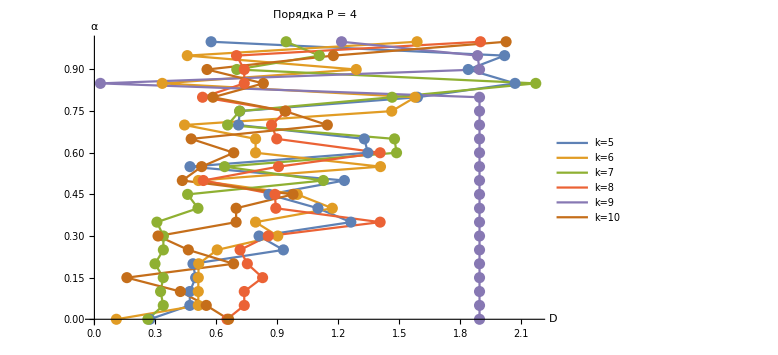

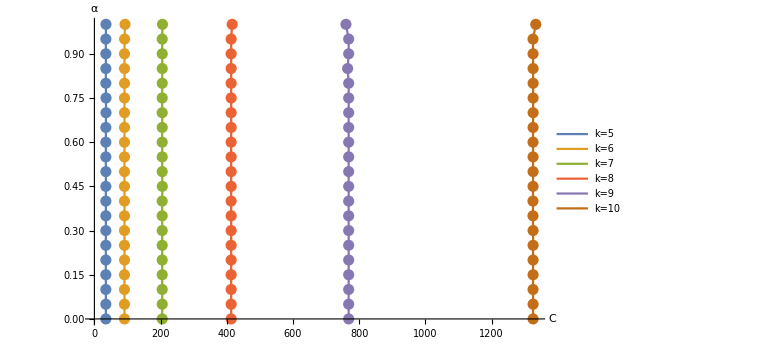

```mathematica
ListLinePlot[Table[data4interl500[[x,All,{2,1}]],{x,1,6}],Joined->True,PlotLegends->{"k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[D],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All,PlotLabel->Style["Порядка P = 4",18]]
ListLinePlot[Table[data4interl500[[x,All,{3,1}]],{x,1,6}],Joined->True,PlotLegends->{"k=5","k=6","k=7","k=8","k=9","k=10"},AxesLabel->{HoldForm[C],HoldForm[α]},LabelStyle->{12,GrayLevel[0]},PlotStyle->Thick,PlotRange->All,ImageSize->Large,AxesOrigin->{0.,0.},Mesh->All]
```

```mathematica
datak2to10o2[[3]]
```

{{0.,0.230542,15.},{0.05,1.79569,15.0028},{0.1,1.7978,15.0059},{0.15,1.80016,15.0094},{0.2,1.80284,15.0133},{0.25,1.80588,15.0177},{0.3,1.80928,15.0226},{0.35,1.8133,15.0284},{0.4,1.81811,15.0353},{0.45,1.82364,15.0432},{0.5,1.83049,15.053},{0.55,1.83884,15.0647},{0.6,1.84936,15.0794},{0.65,1.86295,15.098},{0.7,1.88174,15.1234},{0.75,1.93225,15.5988},{0.8,2.39925,15.7213},{0.85,2.46703,15.7397},{0.9,2.50873,15.7553},{0.95,2.89255,16.0029},{1.,3.78885,16.5208}}